```mathematica
Orbit plots for given n values:
```

For n=+1:  (spring potential):

Attractive case:

{u[t]+u''[t]==10/u[t]^3}

{u[0]==1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==10/u[t]^3} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==10/u[t]^3}},{u}]

{{u→InterpolatingFunction[…]}}

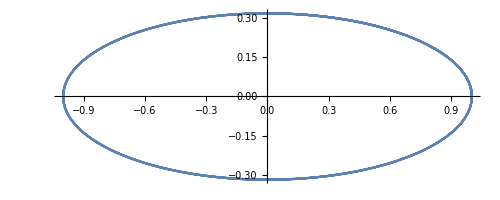

```mathematica
s={u''[t]+u[t]== 10/(u[t])^3}
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,20}]]
```

Repulsive Case:

{u[t]+u''[t]==-1/u[t]^3}

{u[0]==10,u'[0]==0.1}

Solve::naqs: {u[t]+u''[t]==-1/u[t]^3} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==-1/u[t]^3}},{u}]

NDSolve::ndsz: At t == -1.5508, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.5708, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[…]}}

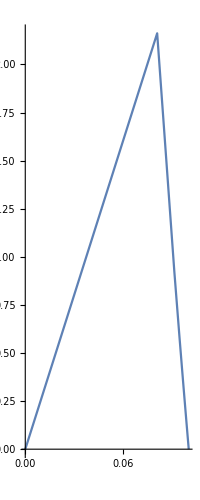

```mathematica
s={u''[t]+u[t]== -1/(u[t])^3}
ics= {u[0]==10,u'[0]==0.1}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]
```

For n = -1 (Constant potential or No force):

{u[t]+u''[t]==0}

{u[0]==0.1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==0} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==0}},{u}]

{{u→InterpolatingFunction[…]}}

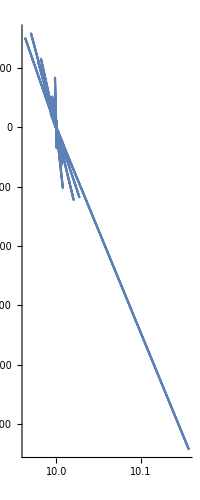

```mathematica
s={u''[t]+u[t]== 0}
ics= {u[0]==0.1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]
```

For n = -2 (Keplar Problem):

Attractive potential (plotted for E<0)

{u[t]+u''[t]==5}

{u[0]==1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==5} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==5}},{u}]

{{u→InterpolatingFunction[…]}}

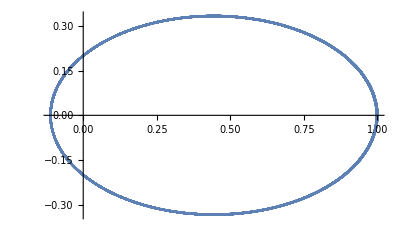

```mathematica
s={u''[t]+u[t]==5}
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]
```

Repulsive Potential:

{u[t]+u''[t]==-1}

{u[0]==1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==-1} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==-1}},{u}]

{{u→InterpolatingFunction[…]}}

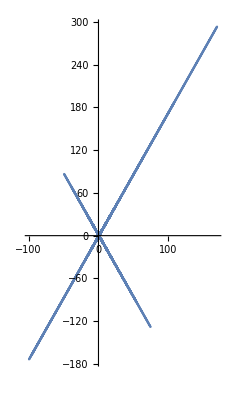

```mathematica
s={u''[t]+u[t]==-1}
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]
```

For n = -3 :

Attractive Case:

{u[t]+u''[t]==1.01 u[t]}

{u[0]==1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==1.01 u[t]} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==1.01 u[t]}},{u}]

{{u→InterpolatingFunction[…]}}

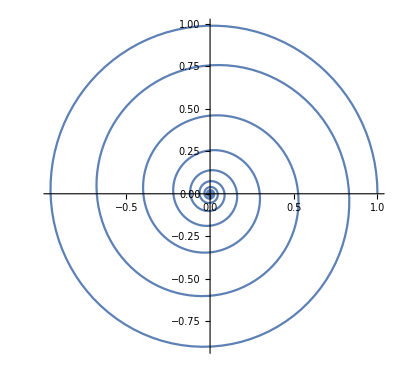

```mathematica
s={u''[t]+u[t]==1.01(u[t]) }
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol],{t,0,200},PlotRange->Full]
```

Repulsive Case:

{u[t]+u''[t]==0.99 u[t]}

{u[0]==1,u'[0]==0}

Solve::naqs: {u[t]+u''[t]==0.99 u[t]} is not a quantified system of equations and inequalities.

Solve[{{u[t]+u''[t]==0.99 u[t]}},{u}]

{{u→InterpolatingFunction[…]}}

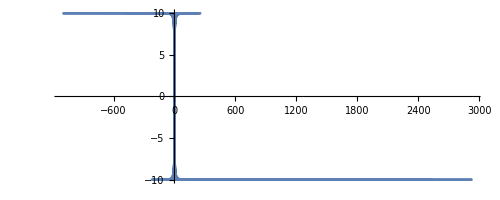

```mathematica
s={u''[t]+u[t]== 0.99(u[t]) }
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol],{t,0,200}]
```